### Autonomous Equations :

```mathematica
Eqx=1/2 (3 (-1+w) x[η]^3-√6 λ y[η]^2-3 x[η] (1-w+(1+w) y[η]^2));
Eqy=-1/2 y[η] (√6 λ x[η]-3 (-1+w) x[η]^2+3 (1+w) (-1+y[η]^2));
```

```mathematica
ex=Eqx/.x_[η]->x
ey=Eqy/.x_[η]->x
```

1/2 (3 (-1+w) x^3-3 x (1-w+(1+w) y^2)-√6 y^2 λ)

-1/2 y (-3 (-1+w) x^2+3 (1+w) (-1+y^2)+√6 x λ)

### Cosmological parameters in terms of dimensionless variables :

```mathematica
Ωphi=-x^2+y^2;
Ωm=1-Ωphi;
wphi=(-x^2-y^2)/(-x^2+y^2);
weff=Ωphi*wphi + Ωm *w ;
w=0;
λ=1;
```

### Phase Space Boundary : Ωm ≥ 0 => (x^2 + y^2 ≤ 1)

```mathematica
boundsf=RegionPlot[y^2-x^2<1&&y>0,{x,-5,5},{y,0,4},PlotStyle->None,BoundaryStyle->Thickness[0.003]];
```

### Critical points:

```mathematica
cp=Graphics[{PointSize[0.02],Point[{0,0}], Point [{1,0}], Point[{-1,0}],Red,Point[{-λ/(√6),√((6+λ^2)/6)}]}];
```

```mathematica
Heteroclinic orbit
```

```mathematica
nsol=NDSolve[Evaluate[{{Eqx==x'[η],Eqy==y'[η]}, x[0]==0,y[0]==0.01}], {x[η], y[η]}, {η, 0, 100},MaxSteps->10^5,StartingStepSize->0.001,MaxStepFraction->1/1000]
```

{{x[η]→InterpolatingFunction[…][η],y[η]→InterpolatingFunction[…][η]}}

### Parametric Plot

```mathematica
pt=ParametricPlot[Evaluate[
{Re[x[η]],Re[y[η]]}/.nsol[[1]]],
 {η,0, 100},PlotPoints -> 200,PlotStyle->{Red,Thick,Dashed}];
```

#### Point labels:

```mathematica
labelsf=Graphics[{Text[Style["A",40],{0,0},{-1,-1}], Text[Style["B",40],{-λ/(√6),(√(6+λ^2))/(√6)},{-1,-1}] }];
```

### Accelerated & Phantom region

```mathematica
phantom=RegionPlot[-x^2+y^2≤1&&y>0&&weff<-1,{x,-2,2},{y,0,2},PlotPoints->100,PlotStyle->RGBColor[0.45, 1, 0.4],BoundaryStyle->None,Frame->True,Axes->False,FrameLabel->{X,Y},FrameStyle->30,RotateLabel->False,AspectRatio->1/2,ImageSize->1000];
acc=RegionPlot[-x^2+y^2≤1&&y>0&&-1<weff<-1/3,{x,-2,2},{y,0,2},PlotPoints->50,PlotStyle->{Yellow},BoundaryStyle->None,Frame->True,Axes->False,FrameLabel->{X,Y},FrameStyle->30,RotateLabel->False,AspectRatio->1/2,ImageSize->1000];
```

Stream Plot:

```mathematica
st=StreamPlot[{ex,ey},{x,-2,2},{y,0,2},RegionFunction->Function[{X,Y},Y^2-X^2<1&&Y>0],AspectRatio->1/2,ImageSize->1000,Frame->True,Axes->False,FrameLabel->{x,y},FrameStyle->30,RotateLabel->False];
```

#### Display ( Check order inside Show[], you might get streamlines masked by standard acceleration & Phantom region)

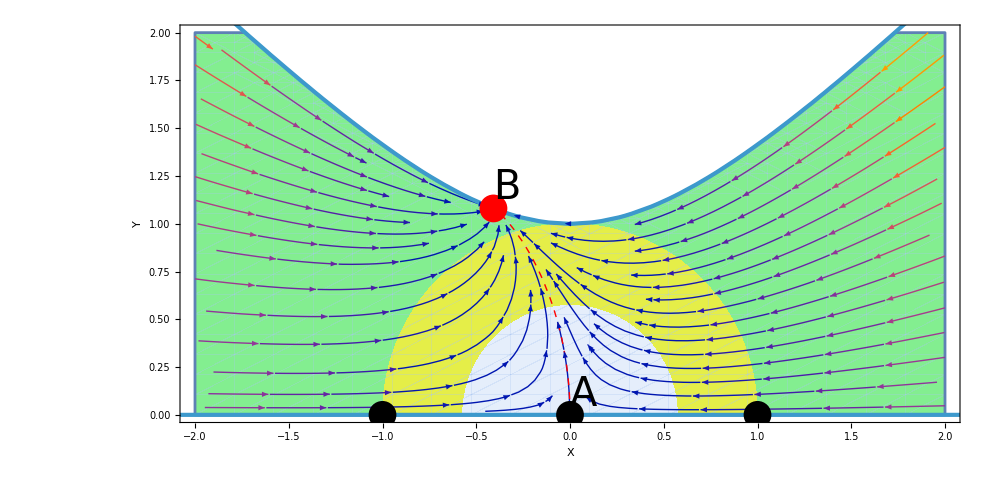

```mathematica
Show[phantom, acc,st,pt,boundsf,cp,labelsf]
```

```mathematica
Anil= Show[phantom, acc,st,pt,boundsf,cp,labelsf]
```

-Graphics-

#### For MAC

```mathematica
Export["~/Desktop/Phantomplot.pdf",Rasterize[Anil,ImageResolution->300]]  (* Rasterize is for no cracks on image while exporting image*)
```

~/Desktop/Phantomplot.pdf

#### For Windows

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","Phantomplot.pdf"}],Rasterize[Anil,ImageResolution->300]]
```

C:\Users\SXC\Desktop\Phantomplot.pdf